# RunLengthRandomnessTest

Conducts a runs up-based randomness test on a sequence of random reals between 0 and 1.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
runsup[seq_]:=Split[seq,#1<#2&];
$meanRunLengths=1.9997972637403931;
stat[seq_]:=Total[(Length/@runsup[seq]-$meanRunLengths)^2/($meanRunLengths)];
statdistμ[seqleng_]:=0.21819458420310864 seqleng(*Need to recalculate with more points and a larger sample size*);
statdistσ[seqleng_]:=0.4208000593890539 seqleng^0.503677726169205(*Need to recalculate with more points and a larger sample size*);
RunLengthRandomnessTest::seqlength="List length is less than 600";
RunLengthRandomnessTest[seq_List/;Length[seq]<600]:=Message[RunLengthRandomnessTest::seqlength];
RunLengthRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&]]:=Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[Length[seq]],statdistσ[Length[seq]]],stat[seq]];
RunLengthRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&],"PValue"]:=2 (*Should this two be here? We're performing a two tailed test. I think it should be here. *)Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[Length[seq]],statdistσ[Length[seq]]],stat[seq]];
RunLengthRandomnessTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&],"TestStatistic"]:=stat[seq];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

RunLengthRandomnessTest[sequence]

uses lengths of runs up to test the randomness of sequence and returns an associated p-value.

RunLengthRandomnessTest[sequence,"property"]

uses lengths of runs up to test the randomness of sequence and reutnrs an associated property.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Properties include

"TestStatistic" | Returns the test statistic
"PValue" | Returns the p-value associated with the test

The test statistic is generated by creating a chi square-like statistic that measures the difference between the lengths of runs up in a sequence and the expected mean lengths of runs up in the sequence.

The test only works for sequences of of random reals between 0 and 1.

RunLengthRandomnessTest results are valid only for sequence lengths greater than 600.

The RunLengthRandomnessTest function performs a two-tailed test on the test statistic.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate a sequence of random integers and apply a run length-based test:

```mathematica
sequence=RandomReal[{0,1},1000];
```

Visualize the sequence:

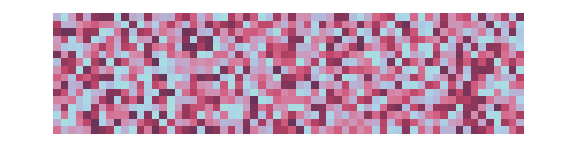

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
RunLengthRandomnessTest[sequence,"TestStatistic"]
```

214.019

```mathematica
RunLengthRandomnessTest[sequence,"PValue"]
```

0.37984

### Scope

Reject the randomness of a non-random sequence:

```mathematica
subsequence=RandomReal[{0,1},100];
```

```mathematica
sequence=Flatten[Table[subsequence,20]];
```

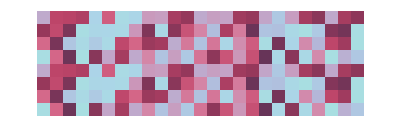

```mathematica
ArrayPlot[Partition[Take[sequence,200],25],]
```

```mathematica
RunLengthRandomnessTest[sequence,"TestStatistic"]
```

299.982

```mathematica
RunLengthRandomnessTest[sequence,"PValue"]
```

9.03216×10^-13

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

Visualize the sampling distribution of the test statistic:

```mathematica
samp=RunLengthRandomnessTest[#,"TestStatistic"]&/@RandomReal[{0,1},{1000,1000}];
```

```mathematica
Histogram[samp,Automatic,"PDF"]
```

-Graphics-

```mathematica
dist=FindDistribution[samp,TargetFunctions->{NormalDistribution}]
```

NormalDistribution[218.579,15.1694]

```mathematica
Show[Histogram[samp,Automatic,"PDF"],Plot[PDF[dist,x],{x,0,300},PlotRange->All]]
```

-Graphics-

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Emmy/Noah Blumenthal
noahb320@gmail.com
emmyb320@bu.edu

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Randomness

Statistics

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

DistributionFitTest

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

OPERM5RandomnessTest

ChiSquareRandomnessTest

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Knuth, Donald E. The Art of Computer Programing.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Wikipedia

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.